# CreateResourceFunctionSymbols

Create a symbol reference for each named resource function

## Definition

```mathematica
CreateResourceFunctionSymbols // ClearAll;
```

### Initialization

```mathematica
$inDef = False;
$debug = True;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::unfinished = "\
Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
CreateResourceFunctionSymbols::internal =
"An unexpected error occurred. `1`";
```

```mathematica
CreateResourceFunctionSymbols::exctx =
"Cannot set definitions in excluded context `1`.";
```

```mathematica
CreateResourceFunctionSymbols::invctx =
"Valid context string expected at position `1` in `2`.";
```

```mathematica
CreateResourceFunctionSymbols::invname =
"Expected a valid ResourceFunction name instead of `1`.";
```

```mathematica
CreateResourceFunctionSymbols::invnames =
"String or list of strings expected at position `1` in `2`.";
```

```mathematica
CreateResourceFunctionSymbols::loadfail =
"Failed to retrieve definitions for the resource function `1`.";
```

```mathematica
CreateResourceFunctionSymbols::locked =
"Cannot set definitions for locked symbol `1`.";
```

```mathematica
CreateResourceFunctionSymbols::symname =
"Cannot get SymbolName of `1`.";
```

```mathematica
CreateResourceFunctionSymbols::symctx =
"Cannot get Context of `1`.";
```

```mathematica
CreateResourceFunctionSymbols::deffail =
"Failed to set definitions for `1`.";
```

```mathematica
CreateResourceFunctionSymbols::invexc =
"Expected a list of contexts or Automatic instead of `1` as the setting for ExcludedContexts.";
```

```mathematica
CreateResourceFunctionSymbols::invow =
"Expected True or False instead of `1` as the setting for OverwriteTarget.";
```

```mathematica
CreateResourceFunctionSymbols::invunk =
"Expected True or False instead of `1` as the setting for AllowUnknownNames.";
```

```mathematica
CreateResourceFunctionSymbols::names =
"Failed to retrieve resource function names.";
```

```mathematica
CreateResourceFunctionSymbols::rsbnames =
"Failed to retrieve resource function names using the ResourceSystemBase `1`.";
```

```mathematica
CreateResourceFunctionSymbols::unkname =
"`1` is not a known resource function name.";
```

```mathematica
CreateResourceFunctionSymbols::unknames =
"`1` are not known resource function names.";
```

### Attributes

```mathematica
CreateResourceFunctionSymbols // Attributes = { };
```

### Options

```mathematica
CreateResourceFunctionSymbols // Options = {
    "AllowUnknownNames" -> True,
    ExcludedContexts    -> Automatic,
    OverwriteTarget     -> False,
    ResourceSystemBase  -> Automatic
};
```

### Argument patterns

```mathematica
$contextString = _String? contextQ;
$anyContext    = Automatic | $contextString;
$symName       = _String? symbolNameQ;
$name          = _String? rfNameQ;
$names         = { $name... };
$nameOrNames   = $name | $names | Automatic | All;
$failure       = _Failure? FailureQ;
$result        = $symName | Missing[ "SymbolExists", $symName ] | $failure;
```

### Main definition

#### Create symbols

Use Automatic as default first argument:

```mathematica
CreateResourceFunctionSymbols[ opts: OptionsPattern[ ] ] :=
    catchTop @ CreateResourceFunctionSymbols[ Automatic, opts ];
```

Use All as default second argument:

```mathematica
CreateResourceFunctionSymbols[ ctx: $anyContext, opts: OptionsPattern[ ] ] :=
    catchTop @ CreateResourceFunctionSymbols[ ctx, All, opts ];
```

Do the thing:

```mathematica
CreateResourceFunctionSymbols[
    ctx0: $anyContext,
    names: $nameOrNames,
    opts: OptionsPattern[ ]
] := catchTop @ Enclose[
    Module[ { ctx, rsbase, unk, base, full, overwrite, excluded, current, res },

        excluded  = OptionValue @ ExcludedContexts;
        ctx       = checkContext[ ctx0, excluded ];
        rsbase    = OptionValue @ ResourceSystemBase;
        unk       = OptionValue @ AllowUnknownNames;
        base      = toNameList[ names, rsbase, unk ];
        full      = (ctx <> #1 &) /@ base;
        overwrite = checkOverwriteTarget @ OptionValue @ OverwriteTarget;
        current   = If[ overwrite, { }, definedNamePatt @ full ];

        res       = Block[ { $existingNames = current },
                           ConfirmMatch[ defineRFSymbols @ full,
                                         { $result... }
                           ]
                    ];

        If[ StringQ @ names,
            ConfirmMatch[ First[ res, $Failed ], $result ],
            res
        ];

        ConfirmMatch[ makeResult @ res, _Success|$failure ]
    ],
    throwInternalFailure[
        CreateResourceFunctionSymbols[ ctx0, names, opts ],
        ##
    ] &
];
```

#### Additional operations

List created symbols:

```mathematica
CreateResourceFunctionSymbols[
    ctx0: $anyContext,
    names: $nameOrNames,
    "List"|List,
    opts: OptionsPattern[ ]
] := catchTop @ Enclose[
    Module[ { ctx, res },
        ctx = checkContext[ ctx0, None ];
        res = listRFSymbols[ ctx, names ];
        ConfirmMatch[ res, { ___String? fullNameQ } ]
    ],
    throwInternalFailure[
        CreateResourceFunctionSymbols[ ctx0, names, opts ],
        ##
    ] &
];
```

Remove created symbols:

```mathematica
CreateResourceFunctionSymbols[
    ctx0: $anyContext,
    names: $nameOrNames,
    "Remove"|Remove,
    opts: OptionsPattern[ ]
] := catchTop @ Enclose[
    Module[ { before, removed, after },
        before = CreateResourceFunctionSymbols[ ctx0, names, "List", opts ];
        ConfirmMatch[ before, { ___String? fullNameQ } ];
        removed = Remove @@ before;
        after = CreateResourceFunctionSymbols[ ctx0, names, "List", opts ];
        ConfirmMatch[ after, { ___String? fullNameQ } ];
        If[ after === { },
            Success[
                "CreateResourceFunctionSymbols",
                <|
                    "MessageTemplate"   -> "Removed `1` symbols.",
                    "MessageParameters" -> { Length @ before },
                    "Tag"               -> "CreateResourceFunctionSymbols",
                    "Removed"           -> before,
                    "Failed"            -> after
                |>
            ],
            Failure[
                "CreateResourceFunctionSymbols",
                <|
                    "MessageTemplate"   -> "Failed to remove `1` symbols.",
                    "MessageParameters" -> { Length @ after },
                    "Tag"               -> "CreateResourceFunctionSymbols",
                    "Removed"           -> before,
                    "Failed"            -> after
                |>
            ]
        ]
    ],
    throwInternalFailure[
        CreateResourceFunctionSymbols[ ctx0, names, opts ],
        ##
    ] &
];
```

### Error cases

First argument is not a valid context:

```mathematica
e: CreateResourceFunctionSymbols[ Except[ $anyContext ], ___ ] :=
    catchTop @ throwFailure[ "invctx", 1, HoldForm @ e ];
```

Second argument is not a valid list of names:

```mathematica
e: CreateResourceFunctionSymbols[ $anyContext, Except[ $nameOrNames ], ___ ] :=
    catchTop @ throwFailure[ "invnames", 2, HoldForm @ e ];
```

Wrong number of arguments:

```mathematica
e: CreateResourceFunctionSymbols[ _, _, a: Except[ OptionsPattern[ ] ], ___ ] :=
    catchTop @ throwFailure[ "nonopt", a, 2, HoldForm @ e ];
```

Missed something that needs to be fixed:

```mathematica
e: CreateResourceFunctionSymbols[ ___ ] :=
    catchTop @ throwInternalFailure @ e;
```

### Dependencies

```mathematica
$defaultContext := "RF`";
$existingNames  := { };
$localNames     := getLocalCachedNames[ ];
```

#### Misc utilities

##### makeResult

```mathematica
makeResult // beginDefinition;
```

```mathematica
makeResult[ res: { ___, $failure, ___ } ] := Enclose[
    Module[ { created, exists, failed, other },

        created = Cases[ res, $symName ];
        exists  = Cases[ res, Missing[ "SymbolExists", $symName ] ];
        failed  = Cases[ res, $failure ];
        other   = Complement[ res, created, exists, failed ];

        ConfirmAssert[ other === { } ];

        Failure[
            "CreateResourceFunctionSymbols",
            <|
                "MessageTemplate"   -> "Failed to create `1` symbols.",
                "MessageParameters" -> { Length @ failed },
                "Created"           -> created,
                "Exists"            -> exists,
                "Failed"            -> failed
            |>
        ]
    ],
    throwInternalFailure[ makeResult @ res, ## ] &
];
```

```mathematica
makeResult[ res: { $result.. } ] := Enclose[
    Module[ { created, exists, failed, other, createdC, existsC, failedC, msg },

        created = Cases[ res, $symName ];
        exists  = Cases[ res, Missing[ "SymbolExists", $symName ] ];
        failed  = ConfirmMatch[ Cases[ res, $failure ], { } ];
        other   = Complement[ res, created, exists, failed ];

        ConfirmAssert[ other === { } ];

        createdC = Length @ created;
        existsC  = Length @ exists;
        failedC  = Length @ failed;

        msg = ConfirmBy[ successMsg[ createdC, existsC, failedC ], StringQ ];

        Success[
            "CreateResourceFunctionSymbols",
            <|
                "MessageTemplate"   -> msg,
                "MessageParameters" -> { createdC, existsC, failedC },
                "Tag"               -> "CreateResourceFunctionSymbols",
                "Created"           -> created,
                "Exists"            -> exists,
                "Failed"            -> failed
            |>
        ]
    ],
    throwInternalFailure[ makeResult @ res, ##1 ] &
];
```

```mathematica
makeResult[ { } ] (* TODO *)
```

```mathematica
makeResult // endDefinition;
```

##### successMsg

```mathematica
successMsg // beginDefinition;
```

```mathematica
successMsg[ cr_Integer? NonNegative, ex_Integer? NonNegative, 0 ] :=
    Module[ { msg1, msg2, msg },

        msg1 = Replace[ cr,
                        {
                            1 -> "Created `1` symbol",
                            _ :> "Created `1` symbols"
                        }
               ];

        msg2 = Replace[ ex,
                        {
                            0 -> "",
                            1 -> "(`2` symbol already exists)",
                            _ :> "(`2` symbols already exist)"
                        }
               ];

        StringTrim[ msg1 <> " " <> msg2 ] <> "."
    ];
```

```mathematica
successMsg // endDefinition;
```

##### listRFSymbols

```mathematica
listRFSymbols // beginDefinition;
```

```mathematica
listRFSymbols[ ctx_? contextQ, allowed0: $names ] := Enclose[
    Module[ { allowed, names, ov, assoc },
        FirstCase[
            allowed,
            name_String /; StringContainsQ[ name, "`" ] :>
                throwFailure[ "invname", name ]
        ];
        allowed = ConfirmMatch[ ctx <> #& /@ allowed0, { $symName... } ];
        names   = ConfirmMatch[ fullNames[ ctx <> "*" ], { ___String } ];
        names   = ConfirmMatch[ Intersection[ names, allowed ], { ___String } ];
        ov      = ToExpression[ names, InputForm, OwnValues ];
        assoc   = ConfirmBy[ AssociationThread[ names -> ov ], AssociationQ ];
        Keys @ Select[ assoc, rfDefQ ]
    ],
    throwInternalFailure[ listRFSymbols @ ctx, ## ] &
];
```

```mathematica
listRFSymbols[ ctx_? contextQ, All|Automatic ] :=
    listRFSymbols[ ctx, Last /@ StringSplit[ Names[ ctx <> "*" ], "`" ] ];
```

```mathematica
listRFSymbols[ ctx_? contextQ, name: $name ] :=
    listRFSymbols[ ctx, { name } ];
```

```mathematica
listRFSymbols // endDefinition;
```

##### fullNames

```mathematica
fullNames // beginDefinition;
```

```mathematica
fullNames[ args___ ] :=
    With[ { ctx = "$" <> StringDelete[ CreateUUID[ ], "-" ] <> "`" },
        Block[ { $Context = ctx, $ContextPath = { ctx } }, Names @ args ]
    ];
```

```mathematica
fullNames // endDefinition;
```

##### fullNameQ

```mathematica
fullNameQ // beginDefinition;
```

```mathematica
fullNameQ[ name_String? NameQ ] :=
    StringMatchQ[ name, Except[ "`" ] ~~ ___ ~~ "`" ~~ ___ ];
```

```mathematica
fullNameQ[ name_ ] := False;
```

```mathematica
fullNameQ // endDefinition;
```

##### rfDefQ

```mathematica
rfDefQ // beginDefinition;
rfDefQ[ def_ ] := ! FreeQ[ def, CreateResourceFunctionSymbols ];
rfDefQ // endDefinition;
```

##### checkOverwriteTarget

```mathematica
checkOverwriteTarget // beginDefinition;
checkOverwriteTarget[ bool: True|False ] := bool;
checkOverwriteTarget[ other_ ] := throwFailure[ "invow", other ];
checkOverwriteTarget // endDefinition;
```

##### checkContext

```mathematica
checkContext // beginDefinition;
```

```mathematica
checkContext[ Automatic, excl_  ] := checkContext[ $defaultContext, excl ];
```

```mathematica
checkContext[ ctx_, Automatic   ] := checkContext[ ctx, $defaultExcluded ];
```

```mathematica
checkContext[ ctx_, None        ] := checkContext[ ctx, { }              ];
```

```mathematica
checkContext[ ctx_? contextQ, excl: { ___? StringPattern`StringPatternQ } ] :=
    If[ StringMatchQ[ ctx, # <> "*" & /@ StringTrim[ excl, "*" ] ],
        throwFailure[ "exctx", ctx ],
        ctx
    ];
```

```mathematica
checkContext[ ctx_, excl_? StringPattern`StringPatternQ ] :=
    checkContext[ ctx, { excl } ];
```

```mathematica
checkContext[ _, other_ ] := throwFailure[ "invexc", other ];
```

```mathematica
checkContext // endDefinition;
```

##### toNameList

```mathematica
toNameList // beginDefinition;
```

```mathematica
toNameList[ _, _, inv: Except[ True|False ] ] := throwFailure[ "invunk", inv ];
```

```mathematica
toNameList[ All | Automatic, rsb_, _ ] := getResourceFunctionNames @ rsb;
```

```mathematica
toNameList[ name: $name, rsb_, unk_ ] := toNameList[ { name }, rsb, unk ];
```

```mathematica
toNameList[ names: { $name... }, rsb_, True ] := names;
```

```mathematica
toNameList[ names: { $name... }, rsb_, False ] :=
    Module[ { known, unknown },
        known = getResourceFunctionNames @ rsb;
        unknown = Complement[ names, known ];
        Replace[
            unknown,
            {
                { }         :> names,
                { unk_ }    :> throwFailure[ "unkname" , unk ],
                unk: { __ } :> throwFailure[ "unknames", Short @ unk ],
                ___         :> throwInternalFailure @
                                   toNameList[ names, rsb, False ]
            }
        ]
    ];
```

```mathematica
toNameList // endDefinition;
```

##### definedNamePatt

```mathematica
definedNamePatt // beginDefinition;
```

```mathematica
definedNamePatt[ names: { ___String } ] := Apply[
    Alternatives,
    ToExpression[ Select[ names, definedNameQ ], InputForm, HoldPattern ]
];
```

```mathematica
definedNamePatt // endDefinition;
```

##### defineRFSymbols

```mathematica
defineRFSymbols // beginDefinition;
```

```mathematica
defineRFSymbols[ fullNames_ ] :=
    Quiet[ ToExpression[ fullNames, InputForm, defineRFSymbol ],
           General::shdw
    ];
```

```mathematica
defineRFSymbols // endDefinition;
```

##### qualifiedNames

```mathematica
qualifiedNames // beginDefinition;
```

```mathematica
qualifiedNames[ args___ ] :=
    With[ { ctx = "$" <> StringDelete[ CreateUUID[ ], "-" ] <> "`" },
        Block[ { $Context = ctx, $ContextPath = { ctx } }, Names @ args ]
    ];
```

```mathematica
qualifiedNames // endDefinition;
```

##### definedNameQ

```mathematica
definedNameQ // beginDefinition;
definedNameQ[ name_? NameQ ] := ToExpression[ name, InputForm, definedSymbolQ ];
definedNameQ[ ___ ] := False;
definedNameQ // endDefinition;
```

##### definedSymbolQ

```mathematica
definedSymbolQ // beginDefinition;
definedSymbolQ // Attributes = { HoldAllComplete };
definedSymbolQ[ _Symbol? System`Private`HasAnyEvaluationsQ ] := True;
definedSymbolQ[ _Symbol? System`Private`HasAnyCodesQ       ] := True;
definedSymbolQ[ ___ ] := False;
definedSymbolQ // endDefinition;
```

##### $defaultExcluded

```mathematica
$defaultExcluded // ClearAll;
```

```mathematica
$defaultExcluded :=
    Block[ { $ContextPath },
        Needs[ "ResourceSystemClient`DefinitionUtilities`" ];
        $defaultExcluded =
            FirstCase[
                {
                    ResourceSystemClient`DefinitionUtilities`Private`$defaultExcludedContexts,
                    Language`$InternalContexts
                },
                { __String },
                throwInternalFailure @ $defaultExcluded
            ]
    ];
```

##### symbolNameQ

```mathematica
symbolNameQ // beginDefinition;
symbolNameQ[ name_String? StringQ ] := Internal`SymbolNameQ[ name, True ];
symbolNameQ[ ___ ] := False;
symbolNameQ // endDefinition;
```

##### rfNameQ

```mathematica
rfNameQ // beginDefinition;
rfNameQ[ name_String? StringQ ] := Internal`SymbolNameQ[ name, False ];
rfNameQ[ ___ ] := False;
rfNameQ // endDefinition;
```

##### contextQ

```mathematica
contextQ // beginDefinition;
contextQ[ c_String? StringQ ] := Internal`SymbolNameQ[ c<>"x", True ];
contextQ[ ___ ] := False;
contextQ // endDefinition;
```

##### defineRFSymbol

```mathematica
defineRFSymbol // beginDefinition;
```

```mathematica
defineRFSymbol // Attributes = { HoldFirst };
```

```mathematica
defineRFSymbol[ s_Symbol ] /; MatchQ[ Unevaluated @ s, $existingNames ] :=
    Missing[ "SymbolExists",
             Context @ Unevaluated @ s <> SymbolName @ Unevaluated @ s
    ];
```

```mathematica
defineRFSymbol[ s_Symbol ] /; MemberQ[ Attributes @ s, Locked ] :=
    messageFailure[ CreateResourceFunctionSymbols::locked, HoldForm @ s ];
```

```mathematica
defineRFSymbol[ s_Symbol ] := Enclose[
    defineRFSymbol[ s, ConfirmBy[ SymbolName @ Unevaluated @ s, StringQ ] ],
    messageFailure[ CreateResourceFunctionSymbols::symname, HoldForm @ s ] &
];
```

```mathematica
defineRFSymbol[ s_Symbol, n_String ] := Enclose[
    defineRFSymbol[ s, n, ConfirmBy[ Context @ Unevaluated @ s, StringQ ] ],
    messageFailure[ CreateResourceFunctionSymbols::symctx, HoldForm @ s ] &
];
```

```mathematica
defineRFSymbol[ s_Symbol, n_String, c_String ] := (

    s // Unprotect;
    s // ClearAll;

    s := With[ { rf = ResourceFunction[ n ] },
                If[ FailureQ @ rf,
                    ResourceFunction[ "MessageFailure" ][
                        CreateResourceFunctionSymbols::loadfail,
                        n
                    ],
                    s // Clear;
                    s /; (CreateResourceFunctionSymbols; True) =
                        ResourceFunction[ n, "Function" ]
                ]
            ];

    If[ FreeQ[ OwnValues @ s, CreateResourceFunctionSymbols ],
        messageFailure[ CreateResourceFunctionSymbols::deffail, HoldForm @ s ],
        c <> n
    ]
);
```

```mathematica
defineRFSymbol // endDefinition;
```

##### getResourceFunctionNames

```mathematica
getResourceFunctionNames // beginDefinition;
```

```mathematica
getResourceFunctionNames[ rsb_ ] :=
    Replace[ Quiet @ Union[ wfrNames @ rsb, $localNames ],
             Except[ { __String } ] :> throwFailure[ "names" ]
    ];
```

```mathematica
getResourceFunctionNames // endDefinition;
```

##### wfrNames

```mathematica
wfrNames // beginDefinition;
```

```mathematica
wfrNames[ Automatic ] := wfrNames @ $ResourceSystemBase;
```

```mathematica
wfrNames[ (URL|CloudObject)[ url_String? StringQ, ___ ] ] := wfrNames @ url;
```

```mathematica
wfrNames[ rsb_String? StringQ ] := Enclose[
    Module[ { all, names },
        all = ConfirmBy[ publicResourceInformation[ "Names", rsb ],
                         AssociationQ
              ];
        names = ConfirmMatch[ Lookup[ all, "Function" ], { __String } ];
        wfrNames[ rsb ] = names
    ],
    throwFailure[ "rsbnames", rsb ] &
];
```

```mathematica
wfrNames // endDefinition;
```

##### getLocalCachedNames

```mathematica
getLocalCachedNames // beginDefinition;
```

```mathematica
getLocalCachedNames[ ] :=
    getLocalCachedNames[
        FunctionResource`Autocomplete`Private`$resourceFunctionNames,
        FunctionResource`Autocomplete`Private`$publicNames
    ];
```

```mathematica
getLocalCachedNames[ all_List, public_List ] :=
    Select[ Complement[ all, public ], StringQ ];
```

```mathematica
getLocalCachedNames[ ___ ] := { };
```

```mathematica
getLocalCachedNames // endDefinition;
```

##### publicResourceInformation

```mathematica
publicResourceInformation // ClearAll;
```

```mathematica
publicResourceInformation :=
    Block[ { $ContextPath },
        Needs[ "ResourceSystemClient`" ];
        publicResourceInformation =
            ResourceSystemClient`Private`publicResourceInformation
    ];
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ CreateResourceFunctionSymbols, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[
            quiet @ ResourceFunction[ "MessageFailure" ][ args ],
            $failed = True
        ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[
        CreateResourceFunctionSymbols::internal,
        $bugReportLink,
        HoldForm @ eval,
        a
    ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> SymbolName @ CreateResourceFunctionSymbols
    |>
];
```

## Documentation

### Usage

CreateResourceFunctionSymbols[]

defines a symbol for each named ResourceFunction in "RF`".

CreateResourceFunctionSymbols["ctx`"]

defines symbols in the given context.

CreateResourceFunctionSymbols["ctx`",{name_1,name_2,…}]

only defines symbols for the given names.

### Details & Options

CreateResourceFunctionSymbols[] is equivalent to CreateResourceFunctionSymbols[Automatic].

CreateResourceFunctionSymbols accepts the following options:

OverwriteTarget | False | whether to redefine the target symbol if it already exists
ExcludedContexts | Automatic | a list of contexts that should be protected from changes
ResourceSystemBase | Automatic | the resource system to obtain names from
AllowUnknownNames | True | whether to set definitions for unknown resource names

When OverwriteTarget is set to False, a target symbol will not be redefined if it has any existing definitions.

ExcludedContexts is meant to be a safety mechanism to prevent changing definitions in important system contexts.

ExcludedContexts->None can be used to force CreateResourceFunctionSymbols to define symbols in a system context, but this is not recommended.

When AllowUnknownNames is set to True, CreateResourceFunctionSymbols["ctx`",names] will define symbols for all names, even if they do not correspond to a known resource function name.

## Examples

```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Create symbols for each resource function:

```mathematica
CreateResourceFunctionSymbols[]
```

Success[…]

Use a resource function as a symbol:

```mathematica
RF`BirdSay["neat"]
```

neat

### Scope

Specify the context:

```mathematica
CreateResourceFunctionSymbols["MyContext`"]
```

Success[…]

Use a resource function from the new context:

```mathematica
MyContext`PartyParrot["Birdnardo"]
```

-Graphics-

Define a single resource function:

```mathematica
CreateResourceFunctionSymbols["BirdStuff`","BirdSay"]
```

Success[…]

```mathematica
BirdStuff`BirdSay["neat"]
```

neat

Define a specific set of resource functions:

```mathematica
CreateResourceFunctionSymbols["NewContext`",{"PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
NewContext`SpeechBubble[NewContext`PartyParrot["Birdnardo"], "I'm the new BirdSay", Scaled[.25]]
```

-Graphics-

List symbols created by CreateResourceFunctionSymbols:

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"List"]
```

{NewContext`PartyParrot,NewContext`SpeechBubble}

Other symbols are not included in this list:

```mathematica
NewContext`MyFunction[x_]:=x+1;
```

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"List"]
```

{NewContext`PartyParrot,NewContext`SpeechBubble}

Compare to Names:

```mathematica
Names["NewContext`*"]
```

{NewContext`MyFunction,NewContext`PartyParrot,NewContext`SpeechBubble}

Remove symbols created by CreateResourceFunctionSymbols:

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"Remove"]
```

Success[…]

Other symbols are not removed:

```mathematica
Names["NewContext`*"]
```

{NewContext`MyFunction}

### Options

#### OverwriteTarget

By default, existing symbols with definitions won't be redefined:

```mathematica
EmptyContext`BirdSay[expr_]:=ResourceFunction["SpeechBubble"][Show[LinguisticAssistant, ImageSize -> 75], expr, Scaled[.25]];
```

```mathematica
res=CreateResourceFunctionSymbols["EmptyContext`",{"BirdSay","PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
res["Exists"]
```

{Missing[SymbolExists,EmptyContext`BirdSay]}

The definition is unchanged:

```mathematica
EmptyContext`BirdSay["neat"]
```

-Graphics-neat

Overwrite any existing symbols:

```mathematica
CreateResourceFunctionSymbols["EmptyContext`",{"BirdSay","PartyParrot","SpeechBubble"},OverwriteTarget->True]
```

Success[…]

```mathematica
EmptyContext`BirdSay["neat"]
```

neat

#### ExcludedContexts

By default, some contexts are protected:

```mathematica
CreateResourceFunctionSymbols["System`","ContainsQ"]
```

CreateResourceFunctionSymbols::exctx: Cannot set definitions in excluded context System`.

Failure[…]

Override this protection (at your own risk):

```mathematica
CreateResourceFunctionSymbols["System`","ContainsQ",ExcludedContexts->None]
```

Success[…]

```mathematica
ContainsQ[x+y^z,Power[_,_]]
```

True

```mathematica
ContainsQ[x+y^z,Times[_,_]]
```

False

#### AllowUnknownNames

By default, CreateResourceFunctionSymbol will allow defining symbols for names that are not recognized:

```mathematica
CreateResourceFunctionSymbols["MyContext`","DoesNotExist"]
```

Success[…]

These symbols will fail at run-time if used before the corresponding ResourceFunction exists:

```mathematica
MyContext`DoesNotExist
```

ResourceObject::notfname: The ResourceObject DoesNotExist could not be found.

CreateResourceFunctionSymbols::loadfail: Failed to retrieve definitions for the resource function DoesNotExist.

Failure[…]

Use "AllowUnknownNames"->False to ensure that unrecognized names will cause a failure:

```mathematica
CreateResourceFunctionSymbols["MyContext`","AlsoDoesNotExist","AllowUnknownNames"->False]
```

CreateResourceFunctionSymbols::unkname: AlsoDoesNotExist is not a known resource function name.

Failure[…]

### Applications

Define all resource functions from a particular category:

```mathematica
CreateResourceFunctionSymbols["WFP`",{{"[◼]", "CategoryResourceFunctions"}}["Wolfram Physics Project","Name"]]
```

Success[…]

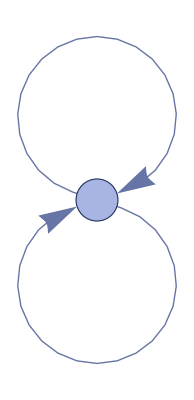
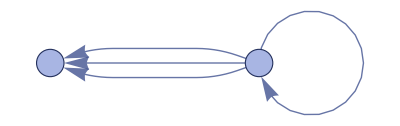
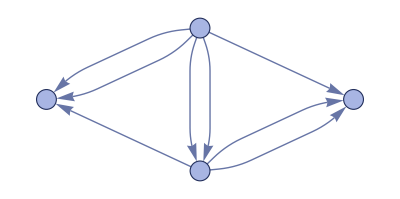
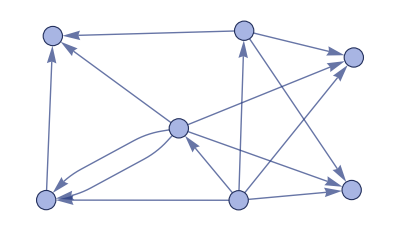
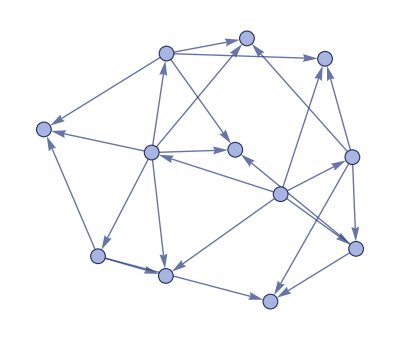
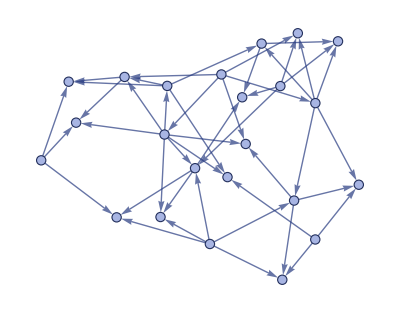

```mathematica
WFP`WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},5,"StatesPlotsList"]
```

```mathematica
WFP`GraphReconstructedSurface[WFP`WolframModel[,{{0,0},{0,0}},10,"FinalState"]]
```

-Graphics3D-

Create symbols in the current context to reference resource functions by their base name:

```mathematica
CreateResourceFunctionSymbols[$Context];
```

```mathematica
FoldRight[f,x,{a,b,c,d}]
```

f[a,f[b,f[c,f[d,x]]]]

```mathematica
Stereogram3D[ResourceData["Stanford Bunny","MeshRegion"],Boxed->True]
```

-Graphics-

```mathematica
StringFunction[Subsets]["string"]
```

{,s,t,r,i,n,g,st,sr,si,sn,sg,tr,ti,tn,tg,ri,rn,rg,in,ig,ng,str,sti,stn,stg,sri,srn,srg,sin,sig,sng,tri,trn,trg,tin,tig,tng,rin,rig,rng,ing,stri,strn,strg,stin,stig,stng,srin,srig,srng,sing,trin,trig,trng,ting,ring,strin,strig,strng,sting,sring,tring,string}

### Properties and Relations

Get the list of created symbols:

```mathematica
res=CreateResourceFunctionSymbols["RedefineTest`",{"BirdSay","PartyParrot"}]
```

Success[…]

```mathematica
res["Created"]
```

{RedefineTest`BirdSay,RedefineTest`PartyParrot}

Symbols that have already been created by CreateResourceFunctionSymbols are returned as Missing objects:

```mathematica
res=CreateResourceFunctionSymbols["RedefineTest`",{"BirdSay","PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
res["Exists"]
```

{Missing[SymbolExists,RedefineTest`BirdSay],Missing[SymbolExists,RedefineTest`PartyParrot]}

```mathematica
res["Created"]
```

{RedefineTest`SpeechBubble}

User-created resource functions will also be included if they are discoverable by name:

```mathematica
DefineResourceFunction[#+1&,"AddOne"]
```

[◼] | AddOne

```mathematica
CreateResourceFunctionSymbols[];
```

```mathematica
RF`AddOne[5]
```

6

Create a resource function symbol:

```mathematica
CreateResourceFunctionSymbols["DefinitionExample`","GrayCode"]
```

Success[…]

Check the definition:

```mathematica
Definition[DefinitionExample`GrayCode]
```

DefinitionExample`GrayCode:=With[{f$=ResourceFunction[GrayCode,Function]},If[FailureQ[f$],ResourceFunction[MessageFailure][CreateResourceFunctionSymbols::loadfail,GrayCode],Clear[DefinitionExample`GrayCode];DefinitionExample`GrayCode/;(CreateResourceFunctionSymbols;True)=f$]]

The definition changes after the symbol is used for the first time:

```mathematica
DefinitionExample`GrayCode[14]
```

{1,0,0,1}

```mathematica
Definition[DefinitionExample`GrayCode]//InputForm//ToString
```

DefinitionExample`GrayCode /; (CreateResourceFunctionSymbols; True) = FunctionRepository`$6c2750db6e7a4e7b83385739b0a46fd7`GrayCode

### Possible Issues

Locked symbols cannot be overwritten:

```mathematica
AnotherContext`BirdSay="nope";
SetAttributes[AnotherContext`BirdSay,Locked];
```

```mathematica
res=CreateResourceFunctionSymbols["AnotherContext`",{"BirdSay","PartyParrot","SpeechBubble"},OverwriteTarget->True]
```

CreateResourceFunctionSymbols::locked: Cannot set definitions for locked symbol AnotherContext`BirdSay.

Failure[…]

```mathematica
res["Created"]
```

{AnotherContext`PartyParrot,AnotherContext`SpeechBubble}

```mathematica
res["Failed"]
```

{Failure[…]}

### Neat Examples

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

all resource functions

define resource functions

initialize resource function

resource symbol

resource function

resource names

symbols

wfr symbols

### Categories

3D Visualization |  Accessibility
 Array Manipulation |  Cloud & Deployment
 Core Language & Structure |  Data Manipulation & Analysis
 Engineering Data & Computation |  External Interfaces & Connections
 Financial Data & Computation |  Geographic Data & Computation
 Geometry |  Graphs & Networks
 Higher Mathematical Computation |  Images
 Just For Fun |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Programming Utilities |  Repository Tools
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |  Wolfram Physics Project

### Related Symbols

ResourceFunction

DefineResourceFunction

ResourceObject

Names

Contexts

InitializationValue

### Related Resource Objects

DistributeResourceFunctions

PacletizeResourceFunction

PersistResourceFunction

RecentResourceFunctions

CategoryResourceFunctions

ResourceFunctionSymbols

CreateResourceObjectGallery

### Source/Reference Citation

Source, reference or citation information

### Links

CreateResourceFunctionSymbols | rhennigan/ResourceFunctions | GitHub

### Tests

#### Initialization

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> True ],
    KeyValuePattern[ "TestMode" -> True ],
    SameTest -> MatchQ
]
```

#### Tests

##### Basic Examples

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ ],
    Success[
        "CreateResourceFunctionSymbols",
        Alternatives[
            KeyValuePattern[ "Created" -> { __String } ],
            KeyValuePattern[ "Exists" -> { __Missing } ]
        ]
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    RF`GrayCode[ 14 ],
    { 1, 0, 0, 1 }
]
```

##### Scope

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "MyContext`" ],
    Success[
        "CreateResourceFunctionSymbols",
        Alternatives[
            KeyValuePattern[ "Created" -> { __String } ],
            KeyValuePattern[ "Exists" -> { __Missing } ]
        ]
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    MyContext`GrayCode[ 14 ],
    { 1, 0, 0, 1 }
]
```

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[
        "NewContext`",
        { "GrayCode", "ColorToHex" }
    ],
    Success[
        "CreateResourceFunctionSymbols",
        Alternatives[
            KeyValuePattern[ "Created" -> { __String } ],
            KeyValuePattern[ "Exists" -> { __Missing } ]
        ]
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    NewContext`GrayCode[ 14 ],
    { 1, 0, 0, 1 }
]
```

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "NewContext`", All, "List" ],
    { ___, "NewContext`ColorToHex", ___, "NewContext`GrayCode", ___ },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    NewContext`MyFunction[ x_ ] := x + 1;
    FreeQ[
        CreateResourceFunctionSymbols[ "NewContext`", All, "List" ],
        "NewContext`MyFunction"
    ],
    True
]
```

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "NewContext`", All, "Remove" ],
    Success[
        "CreateResourceFunctionSymbols",
        KeyValuePattern @ { "Removed" -> { __String }, "Failed" -> { } }
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    Names[ "NewContext`*" ],
    { ___, "NewContext`MyFunction", ___ },
    SameTest -> MatchQ
]
```

##### Options

OverwriteTarget

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "OverwriteTargetTest`", All, "Remove" ],
    Success[
        "CreateResourceFunctionSymbols",
        KeyValuePattern @ { "Removed" -> { ___String }, "Failed" -> { } }
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    OverwriteTargetTest`ColorToHex[ x_ ] := x + 1;
    CreateResourceFunctionSymbols[ "OverwriteTargetTest`", All ];
    OverwriteTargetTest`ColorToHex[ 5 ],
    6
]
```

```mathematica
VerificationTest[
    OverwriteTargetTest`GrayCode[ 14 ],
    { 1, 0, 0, 1 }
]
```

```mathematica
VerificationTest[

    CreateResourceFunctionSymbols[
        "OverwriteTargetTest`",
        All,
        OverwriteTarget -> True
    ];

    StringQ @ OverwriteTargetTest`ColorToHex @ Red,
    True
]
```

ExcludedContexts

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "System`", "ContainsQ" ],
    Failure[ "CreateResourceFunctionSymbols::exctx", _ ],
    { CreateResourceFunctionSymbols::exctx },
    SameTest -> MatchQ
]
```

##### Applications

##### Properties and Relations

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[ "RedefineTest`", All, "Remove" ],
    Success[
        "CreateResourceFunctionSymbols",
        KeyValuePattern @ { "Removed" -> { ___String }, "Failed" -> { } }
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[
        "RedefineTest`",
        { "GrayCode", "ColorToHex" }
    ],
    Success[
        "CreateResourceFunctionSymbols",
        KeyValuePattern[
            "Created" -> { "RedefineTest`GrayCode", "RedefineTest`ColorToHex" }
        ]
    ],
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    CreateResourceFunctionSymbols[
        "RedefineTest`",
        { "GrayCode", "ColorToHex", "AppendSequence" }
    ],
    Success[
        "CreateResourceFunctionSymbols",
        KeyValuePattern @ {
            "Created" -> { "RedefineTest`AppendSequence" },
            "Exists" -> {
                Missing[ "SymbolExists", "RedefineTest`GrayCode" ],
                Missing[ "SymbolExists", "RedefineTest`ColorToHex" ]
            }
        }
    ],
    SameTest -> MatchQ
]
```

##### Possible Issues

##### Neat Examples

##### Error Cases

#### Cleanup

```mathematica
VerificationTest[
    Map[
        CreateResourceFunctionSymbols[ #1, All, "Remove" ] &,
        {
            "RF`",
            "MyContext`",
            "BirdStuff`",
            "NewContext`",
            "EmptyContext`",
            "WFP`",
            "Global`",
            "RedefineTest`",
            "DefinitionExample`"
        }
    ],
    {
        Success[
            "CreateResourceFunctionSymbols",
            KeyValuePattern @ { "Removed" -> { ___String }, "Failed" -> { } }
        ]..
    },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> False ],
    KeyValuePattern[ "TestMode" -> False ],
    SameTest -> MatchQ
]
```

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.